# Moat vs Friedel

## Kernels setup

```mathematica
CloseKernels[];
LaunchKernels[52];
$KernelCount
```

KernelObject::proce: Process ssh -4 -x -o StrictHostKeyChecking=no -o BatchMode=yes -R 54255:localhost:54145 -o ExitOnForwardFailure=yes host.example.com sh -s 4 54255@localhost failed with code 255. Error output:
	ssh: Could not resolve hostname host.example.com: ?????????

52

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\MF_DR\friedel

## T= 0 mean-field

### pion self-energy at p_0=0

#### Feynman parameter integral

```mathematica
feynint=(Integrate[Log[(-p^2(x-1)^2-x p^2+p^2+mq2)/Λ^2],{x,0,1},Assumptions->{p>0,mq2>0,Λ>0}]//TrigToExp//Simplify)//Simplify
```

(-4 p+2 p Log[(169 ρ)/(8 Λ^2)]-√(4 p^2+338 ρ) Log[1-p/(√(p^2+(169 ρ)/2))]+√(4 p^2+338 ρ) Log[1+p/(√(p^2+(169 ρ)/2))])/(2 p)

```mathematica
fint[p_,Λ_,ρ_]:=NIntegrate[Log[(-p^2(x-1)^2-x p^2+p^2+(1/2 h^2 ρ))/Λ^2],{x,0,1}];
pft=1000;
fint[pft,111,10^2/2]
feynint/.{p->pft,Λ->111,ρ->10^2/2}//N
```

2.41303

0.415003

#### bare vacuum contribution (in dim. reg.)

```mathematica
mPi2=-ν + λ ρ;
mq2=1/2 h^2 ρ;

PiPiVacBareFab[p_,ρ_]=(h^2 Nc)/(8 π^2)(mq2(1/ϵ-EulerGamma+1+Log[4 π]-Log[mq2/Λ^2])+1/2 p^2(1/ϵ-EulerGamma+2+Log[4 π]-Log[mq2/Λ^2]+(√(p^2+4 mq2))/p Log[(√(p^2+4 mq2)-p)/(√(p^2+4 mq2)+p)]));
PiPiVacBareShi[p_,ρ_]=(h^2 Nc)/(8 π^2)(mq2(1/ϵ-EulerGamma+1+Log[4 π]-Log[mq2/Λ^2])+1/2 p^2(1/ϵ-EulerGamma+Log[4 π]-feynint));
```

```mathematica
ptest1=1234;
PiPiVacBareFab[ptest1,ρ]/.{Nc->3,h->6.4,ν->20,λ->123,Λ->1000,ϵ->0.0002222,ρ->.001}//N
PiPiVacBareShi[ptest1,ρ]/.{Nc->3,h->6.4,ν->20,λ->123,Λ->1000,ϵ->0.0002222,ρ->.001}//N
```

5.50203×10^9

5.50203×10^9

#### renormalized vacuum contribution (finite p scheme)

```mathematica
PiPiVacRen1[p_,ρ_,Λ_]=-(h^2 Nc)/(8 π^2)(mq2(1/2+Log[mq2/Λ^2])+1/2 p^2(-2+Log[mq2/Λ^2]+(√(p^2+4 mq2))/p Log[(√(p^2+4 mq2)+p)/(√(p^2+4 mq2)-p)]));

PiPiVacRen1p0[ρ_,Λ_]=Limit[PiPiVacRen1[p,ρ1,Λ],p->0]/.ρ1->ρ;
SigmaPiVacRen[p_,ρ_,Λ_]=p^2+mPi2+PiPiVacRen1[p,ρ,Λ]-(PiPiVacRen1[p,ρ0,Λ]-PiPiVacRen1p0[ρ0,Λ])//Simplify;
```

#### in-medium contribution

```mathematica
pF=√(μ^2-mq2);
PiPiMed[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));
(*PiPiMed[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[(p+2 pF)/(p-2pF)]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));*)

(*Kapusta*)
PiPiMedKap[p_,ρ_,μ_]=(Nc h^2)/(24 π^2)(4 μ pF-2 p^2 Log[(pF+μ)^2/mq2]-(μ(4 μ^2-3 p^2))/p Log[((p-2 pF)/(p+2pF))^2]+((2 mq2-p^2) √(p^2+4 mq2))/p Log[(2 μ^2(p^2+2mq2)-2μ p pF √(p^2+4 mq2)-mq2 (p^2+4 mq2))/(2 μ^2(p^2+2mq2)+2μ p pF √(p^2+4 mq2)-mq2 (p^2+4 mq2))]);
```

#### full self-energy

```mathematica
SigmaPi[p_,ρ_,Λ_,μ_]=SigmaPiVacRen[p,ρ,Λ]+PiPiMed[p,ρ,μ]//Simplify;
SigmaPiMS[p_,ρ_,Λ_,μ_]=p^2+mPi2+PiPiVacRen1[p,ρ,Λ]+PiPiMed[p,ρ,μ]//Simplify;
SigmaPiKap[p_,ρ_,Λ_,μ_]=SigmaPiVacRen[p,ρ,Λ]+PiPiMedKap[p,ρ,μ]//Simplify;
```

### parameters & data

#### parameters

```mathematica
Nc=3;
h=65/10;

ν=482^2;
λ=758/10;

mq0=300;
(*mq0=20.216128183;*)
ρ0=(2 mq0^2)/h^2;
```

#### data

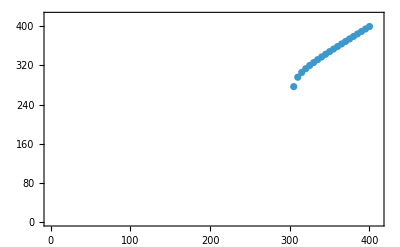

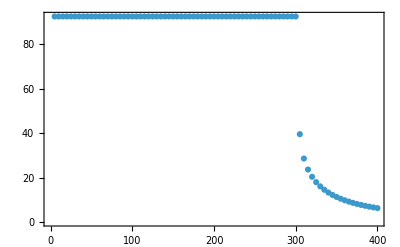

```mathematica
SetDirectory[NotebookDirectory[]];

(*T=1*)
mudat=Flatten[Import["mu.dat"]];
sigmaT1dat=Round[Flatten[Import["sigmaT1.dat"]],10^-15];
rhoT1dat=1/2 sigmaT1dat^2;

sigmaofmuT1=Table[{mudat[[n]],sigmaT1dat[[n]]},{n,Length[mudat]}];
rhoofmuT1=Table[{mudat[[n]],rhoT1dat[[n]]},{n,Length[mudat]}];
mqofmuT1=Table[{mudat[[n]],√(h^2 rhoT1dat[[n]]/2)},{n,Length[mudat]}];
pFofmuT1=Table[{mudat[[n]],√(mudat[[n]]^2-h^2 rhoT1dat[[n]]/2)},{n,Length[mudat]}];

pFT1[n_]:=pF/.{μ->mudat[[n]],ρ->rhoT1dat[[n]]};

(*T=30*)
sigmaT30dat=Round[Flatten[Import["sigma_mu_T30.dat"]],10^-15];
rhoT30dat=1/2 sigmaT30dat^2;

sigmaofmuT30=Table[{mudat[[n]],sigmaT30dat[[n]]},{n,Length[mudat]}];
rhoofmuT30=Table[{mudat[[n]],rhoT30dat[[n]]},{n,Length[mudat]}];
mqofmuT30=Table[{mudat[[n]],√(h^2 rhoT30dat[[n]]/2)},{n,Length[mudat]}];
pFofmuT30=Table[{mudat[[n]],√(mudat[[n]]^2-h^2 rhoT30dat[[n]]/2)},{n,Length[mudat]}];

pFT30[n_]:=pF/.{μ->mudat[[n]],ρ->rhoT30dat[[n]]};

(*T=100*)
sigmaT100dat=Round[Flatten[Import["sigma_mu_T100.dat"]],10^-15];
rhoT100dat=1/2 sigmaT100dat^2;

sigmaofmuT100=Table[{mudat[[n]],sigmaT100dat[[n]]},{n,Length[mudat]}];
rhoofmuT100=Table[{mudat[[n]],rhoT100dat[[n]]},{n,Length[mudat]}];
mqofmuT100=Table[{mudat[[n]],√(h^2 rhoT100dat[[n]]/2)},{n,Length[mudat]}];
pFofmuT100=Table[{mudat[[n]],√(mudat[[n]]^2-h^2 rhoT100dat[[n]]/2)},{n,Length[mudat]}];

pFT100[n_]:=pF/.{μ->mudat[[n]],ρ->rhoT100dat[[n]]};

ListPlot[pFofmuT1,Frame->True,PlotRange->{{0,410},{0,420}}]

ListPlot[{sigmaofmuT1(*,sigmaofmuT30,sigmaofmuT100*)},Frame->True]
```

#### Plots

```mathematica
Length[mudat]
mudat[[61]]
```

80

305

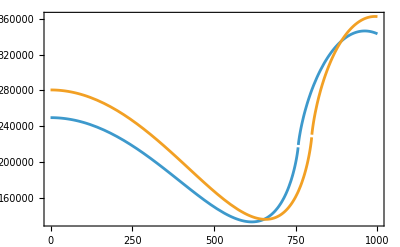

```mathematica
ntest1=61;
ntest2=80;
pFofn[n_]:=pF/.{ρ->rhoT1dat[[n]],μ->mudat[[n]]};
Plot[{SigmaPi[p,rhoT1dat[[ntest1]],mq0,mudat[[ntest1]]],SigmaPi[p,rhoT1dat[[ntest2]],mq0,mudat[[ntest2]]]},{p,0,1000},Frame->True]
```

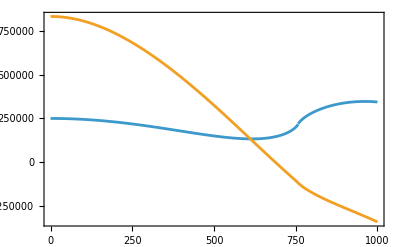

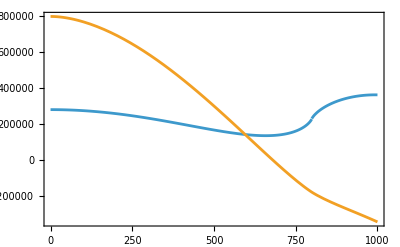

```mathematica
Plot[{SigmaPi[p,rhoT1dat[[ntest1]],mq0,mudat[[ntest1]]],SigmaPiKap[p,rhoT1dat[[ntest1]],mq0,mudat[[ntest1]]]},{p,0,1000},Frame->True,AxesOrigin->{2 pFofn[ntest1],0}]
Plot[{SigmaPi[p,rhoT1dat[[ntest2]],mq0,mudat[[ntest2]]],SigmaPiKap[p,rhoT1dat[[ntest2]],mq0,mudat[[ntest2]]]},{p,0,1000},Frame->True,AxesOrigin->{2 pFofn[ntest2],0}]
```

#### Kapusta

710.493

Power::infy: 碰到无穷表达式 1/0..

FindMinimum::nrnum: 函数值 -∞ 不是位于 {p} = {2.17242×10^11} 的一个实数.

{-1.02218×10^22,{p→1.97493×10^10}}

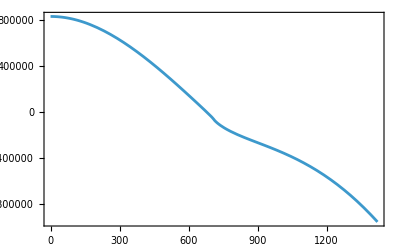

```mathematica
rhotestx=40^2;
mutestx=200;
pFkap =pF/.{ρ->rhotestx,μ->mutestx};
2 pFkap//N
kapfunc=SigmaPiKap[p,rhotestx,mq0,mutestx];
FindMinimum[kapfunc,{p,1.9 pFkap}]
Plot[{kapfunc},{p,0,4 pFkap},Frame->True,AxesOrigin->{2 pFkap,0}]
```

```mathematica
FindMinimum[kapfunc,{p,2 pFkap}]
```

FindMinimum::nrnum: 函数值 Indeterminate 不是位于 {p} = {710.493} 的一个实数.

FindMinimum[kapfunc,{p,2 pFkap}]

#### Fourier trafo

400

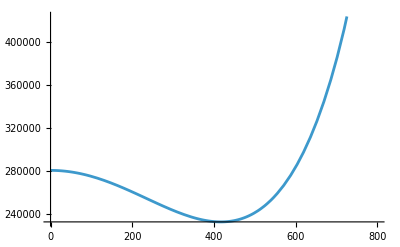

```mathematica
nnn=80;
mudat[[nnn]]
sifu[p_]=SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]];
Plot[sifu[p],{p,0,800}]
pbound=10^7;
sipux[r_]:=NIntegrate[p/(2 π^2) Sin[p r]/r 1/sifu[p],{p,0,27.769398882762918,27.769398882762918*2,27.769398882762918*3,pbound},MaxRecursion->200];
sipux2[r_]:=NIntegrate[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/sifu[p],{p,-pbound,pbound},MaxRecursion->100](*slower*);
(*sipux3[r_]:=1/r InverseFourierTransform[p/(2 π^2)1/sifu[p],p,r];*)
```

```mathematica
NMinimize[Abs[sifu[p+ⅈ q]],{p,q}]
FindRoot[sifu[p],{p,1+ⅈ}]
```

{135764.,{p→657.754,q→-0.0000291901}}

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

{p→618.412+72.5154 ⅈ}

#### Fourier trafo: tests

798.978

FindMinimum::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使函数的值减小得足够多. 您可能需要超过 MachinePrecision 位工作精度以满足这些容差.

657.754

20.2161/pFn[80.]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.05511 and 0.0616858 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -31.6603 and 1.2674 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -14.7821 and 0.00142559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -10.2796 and 0.825553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 9.06009 and 0.259653 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 12.6613 and 0.605756 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.25131 and 0.413906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -10.7072 and 0.386322 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.34748 and 0.483256 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 8.55586 and 0.180736 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.41022 and 0.485498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -6.90039 and 0.00142287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -5.47643 and 0.43487 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 4.56776 and 0.142157 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 6.73471 and 0.346287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.68439 and 0.244009 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -6.61206 and 0.235629 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.712082 and 0.302517 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 5.72086 and 0.115976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.44452 and 0.317031 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -4.51796 and 0.0014275 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -3.73961 and 0.294852 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.03601 and 0.0974881 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 4.57637 and 0.242525 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.28375 and 0.172591 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -4.75109 and 0.169354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.444812 and 0.21911 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 4.28016 and 0.085626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.85239 and 0.235439 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -3.39631 and 0.00142635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.86259 and 0.22319 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.27665 and 0.0740794 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.48966 and 0.186715 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.999782 and 0.133526 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -3.6838 and 0.132391 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.313889 and 0.172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.40476 and 0.0679735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.46823 and 0.187211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.861748 and 0.119909 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.73743 and 0.00142409 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -3.29861 and 0.119439 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.32008 and 0.179585 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.288519 and 0.155309 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.83142 and 0.0596417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.83401 and 0.151892 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.30028 and 0.169906 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.808419 and 0.108889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.50139 and 0.00142312 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -3.00489 and 0.108856 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -7.85002 and 1.41999 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 16.9793 and 0.482605 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 6.45811 and 1.21045 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -24.0287 and 1.76264 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -16.099 and 0.568481 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.369532 and 0.690646 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 13.9901 and 0.250877 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 6.16505 and 0.660353 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -8.80647 and 0.00143012 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -7.62717 and 0.569627 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 5.02113 and 0.183859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 7.81923 and 0.440754 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.4309 and 0.307192 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -8.07622 and 0.292714 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.470923 and 0.371632 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 7.35709 and 0.141272 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.134 and 0.383652 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -5.51256 and 0.00142479 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -4.67602 and 0.351963 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.38577 and 0.115644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 5.3042 and 0.285206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.441 and 0.202082 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -5.39534 and 0.196898 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.397821 and 0.253814 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 4.97692 and 0.0984884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.08799 and 0.270211 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -3.96599 and 0.00142174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -3.33827 and 0.254067 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.55488 and 0.0842129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.97847 and 0.210976 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.06182 and 0.150581 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -4.08689 and 0.148593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.340975 and 0.192735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.77581 and 0.0757733 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.59291 and 0.208587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -3.07272 and 0.00142247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.58096 and 0.199001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.04466 and 0.0660841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 3.16267 and 0.167464 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 8.16549 and 0.517356 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 15.7668 and 1.14369 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -6.60627 and 0.633559 for the integral and error estimates.

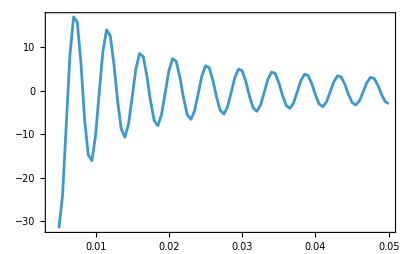

```mathematica
kkkk1=2 pFT1[nnn];
kkkk1//N
kkkk2=p/.FindMinimum[SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]],{p,100}][[2]]
√(mq2/.ρ->rhoT1dat[[nnn]])/pFn[nnn]//N

kkkk=kkkk1;
sipuxlist=ParallelTable[{r,Re[sipux[r]]},{r,.005,.05,.05/100}];
ListPlot[{sipuxlist(*,sipuxlist2*)},Joined->True,Frame->True,PlotRange->All]
```

```mathematica
sipuxlist=ParallelTable[{r,Re[sipux[r]]},{r,.02,.05,.03/80}];
sipuxlist2=ParallelTable[{r,Re[sipux[r]]},{r,.05,.1,.05/100}];
sipuxlist3=ParallelTable[{r,Re[sipux[r]]},{r,.1,.15,.05/100}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -3.00489 and 0.108856 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.244428 and 0.141676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.81578 and 0.056644 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.20554 and 0.155387 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.295 and 0.00142062 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.94455 and 0.150362 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.54232 and 0.0497385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.39227 and 0.128293 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.676859 and 0.0915849 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.54086 and 0.0921854 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.205827 and 0.119982 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.394 and 0.0482189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.01916 and 0.132571 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.97244 and 0.0014193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.66668 and 0.128913 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.33702 and 0.0426672 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.07113 and 0.110428 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.586902 and 0.079134 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.20602 and 0.0801277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.180124 and 0.104238 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.08269 and 0.0421889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.885295 and 0.115733 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.72606 and 0.00141917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.45519 and 0.113047 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.18048 and 0.0373146 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.82255 and 0.0972595 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.521857 and 0.0696329 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.9511 and 0.0708879 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.15927 and 0.0921261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.84526 and 0.0375341 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.7845 and 0.102684 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.53316 and 0.00142001 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.29112 and 0.100663 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.05538 and 0.0331233 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.62479 and 0.0869129 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.471561 and 0.062143 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.7486 and 0.0635811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.140594 and 0.0825216 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.6584 and 0.0338311 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.704836 and 0.0922718 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.37969 and 0.0014209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.16134 and 0.0907323 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.953074 and 0.029753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.46474 and 0.0785689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.430102 and 0.0560915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.58288 and 0.0576633 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.124012 and 0.0747193 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.50664 and 0.0308176 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.639068 and 0.0837803 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.25536 and 0.00141925 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.50849 and 0.0551065 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.0561 and 0.0825888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.10433 and 0.163662 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.69554 and 0.0545021 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.61291 and 0.138917 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.732411 and 0.0995667 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.76359 and 0.100124 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.240806 and 0.130267 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.5754 and 0.0519528 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.1021 and 0.143675 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.11177 and 0.00142179 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.78096 and 0.139377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.44136 and 0.0459403 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.22063 and 0.118458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.636996 and 0.0849105 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.37269 and 0.0857288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.199223 and 0.111562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 2.22827 and 0.044997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.955014 and 0.123582 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.83188 and 0.00142111 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.54849 and 0.120458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.25264 and 0.0398172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.93249 and 0.103423 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.559923 and 0.0740841 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -2.07489 and 0.075219 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.167751 and 0.0978117 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.96244 and 0.0397207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.838219 and 0.108819 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.62067 and 0.0014207 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.36985 and 0.106496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.10939 and 0.0350987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.71278 and 0.0917939 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.497815 and 0.0656796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.84274 and 0.0670314 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.145059 and 0.0870619 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.75124 and 0.0355825 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.744469 and 0.0972002 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.45393 and 0.00141915 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.2267 and 0.0954396 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.997856 and 0.0313511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.53924 and 0.0825288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.448275 and 0.058964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.65823 and 0.0604745 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.128739 and 0.0784287 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.57992 and 0.0322496 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.668903 and 0.0878203 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.31764 and 0.00142341 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.10891 and 0.0864701 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.90811 and 0.0283023 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.39756 and 0.0749796 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.408941 and 0.0534827 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.0561 and 0.0825888 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.86869 and 0.0269891 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.33362 and 0.0717083 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.394682 and 0.0511032 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.44485 and 0.052767 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.110054 and 0.0682655 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.38001 and 0.0283294 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.583311 and 0.0767209 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.15289 and 0.00141899 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.968377 and 0.0758108 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.798694 and 0.0246932 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.22467 and 0.0659592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.364255 and 0.0469248 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.32871 and 0.0486837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.0988352 and 0.062845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.2724 and 0.0262183 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.535887 and 0.0711549 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.06624 and 0.00141953 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.893545 and 0.0700735 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.739984 and 0.0227309 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.13255 and 0.0611148 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.338349 and 0.0434025 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.23016 and 0.045195 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.0898685 and 0.0582178 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.18 and 0.0244868 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.494815 and 0.0657189 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.991434 and 0.00141887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.828787 and 0.0651737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.689864 and 0.0211204 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.0528 and 0.0570961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.316398 and 0.0403114 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.1456 and 0.0422458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.0823986 and 0.0542845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.10016 and 0.022962 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.459824 and 0.0613034 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.926021 and 0.00141897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.772375 and 0.0609612 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.64652 and 0.0195379 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.983976 and 0.0533339 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.297625 and 0.0377648 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.07209 and 0.0396717 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.0758133 and 0.0507443 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.03048 and 0.0214679 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.42952 and 0.0575285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.868545 and 0.00141864 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.723031 and 0.0571695 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.608026 and 0.0182506 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.922954 and 0.0501936 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.281251 and 0.0354174 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.0074 and 0.0373502 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.70107 and 0.0555553 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.0698295 and 0.0477949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.116142 and 0.0713424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.43919 and 0.0295178 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.607634 and 0.0800964 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.20393 and 0.00141883 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.01075 and 0.0790498 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.833443 and 0.025791 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.2789 and 0.0687159 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.377214 and 0.0489162 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.38411 and 0.0506402 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.105371 and 0.0654408 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.3222 and 0.0272391 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.557131 and 0.0736125 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.10773 and 0.00141941 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.928408 and 0.0728291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.769783 and 0.0236759 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.17798 and 0.0634291 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.350294 and 0.0452907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.27853 and 0.0468808 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.0955875 and 0.0604277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.22347 and 0.0253182 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.514434 and 0.0681511 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.02608 and 0.00141918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.85874 and 0.067489 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.71485 and 0.0219068 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.09144 and 0.0589566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.327792 and 0.0418212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.18746 and 0.0436331 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.0867175 and 0.0561931 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.13873 and 0.0237093 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.477443 and 0.063422 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.95632 and 0.00141869 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.799002 and 0.0629985 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.667066 and 0.0202473 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.01714 and 0.0552223 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.307535 and 0.039021 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.10815 and 0.0409033 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.0789344 and 0.0524987 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 1.06488 and 0.0222302 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.444917 and 0.0593907 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.895989 and 0.00141896 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.746973 and 0.059013 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.625645 and 0.0188737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.951851 and 0.0517336 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.289525 and 0.0363592 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -1.03868 and 0.0384282 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.072273 and 0.0492585 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.99998 and 0.0208492 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained 0.416168 and 0.0558044 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in p near {p} = {1396.43}. NIntegrate obtained -0.843001 and 0.00141875 for the integral and error estimates.

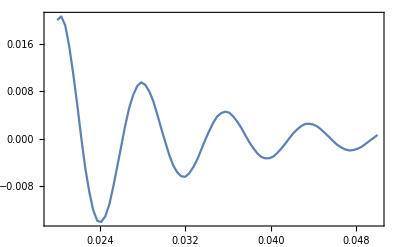

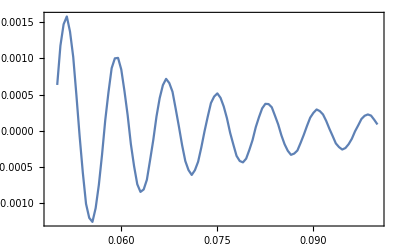

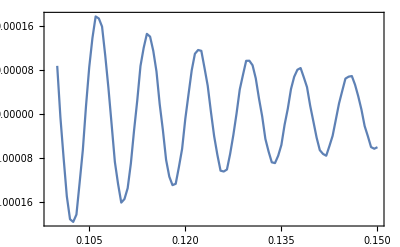

```mathematica
ListPlot[sipuxlist,Joined->True,Frame->True]
ListPlot[sipuxlist2,Joined->True,Frame->True]
ListPlot[sipuxlist3,Joined->True,Frame->True]
```

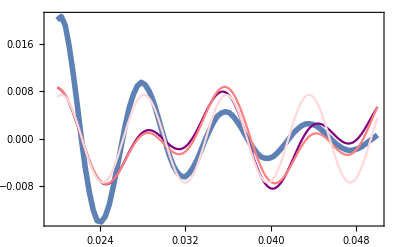

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

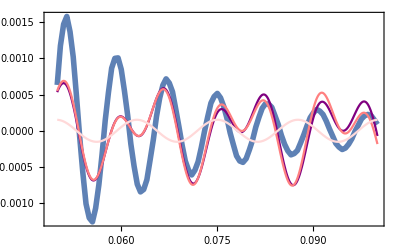

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

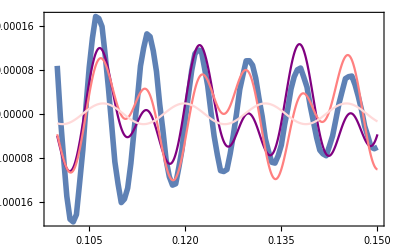

```mathematica
Beatfit[data_]:=Module[{fitfuncbeat,fitfuncbeat2,fitfuncbeat3,beatingfit,beatingfit2,beatingfit3},
fitfuncbeat=a (Sin[kkkk1 (x+b1)]+Sin[kkkk2 (x+b2)]);
fitfuncbeat2=a (Sin[a1 kkkk1 (x+b1)]+Sin[a2 kkkk2 (x+b2)]);
fitfuncbeat3=a Sin[a1 500 x+b1];
beatingfit=FindFit[data,fitfuncbeat,{a,a1, a2,b1,b2},x];
beatingfit2=FindFit[data,fitfuncbeat2,{a,a1, a2,b1,b2},x];
beatingfit3=FindFit[data,fitfuncbeat3,{a,a1, a2,b1,b2},x];
Show[ListPlot[data,Joined->True,Frame->True,PlotStyle->Thickness[.01]],Plot[{fitfuncbeat/.beatingfit,fitfuncbeat2/.beatingfit2,fitfuncbeat3/.beatingfit3},{x,First[data][[1]],Last[data][[1]]},PlotStyle->{Purple,Pink,LightRed},Frame->True]]
]
Beatfit[sipuxlist]
Beatfit[sipuxlist2]
Beatfit[sipuxlist3]
```

#### analytic structure μ=400 MeV

```mathematica
(* pole *)
sifu[p_]=SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]](*+p^2-ν + λ rhoT1dat[[nnn]]*);
```

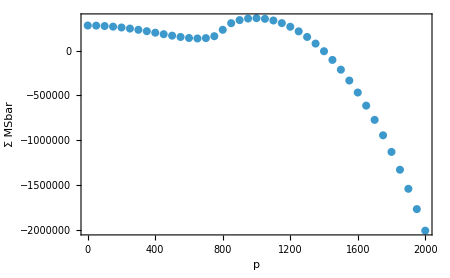

```mathematica
firaa=2000;
fitdat=Table[{p,Re[sifu[p]]},{p,0,firaa,50}];
fifu=a(p^2-p0^2)^2+mm^2;
(*fifupa=FindFit[fitdat,fifu,{a,p0,mm},p]*)
Show[ListPlot[fitdat],Frame->True,FrameLabel->{"p","Σ MSbar"}]
```

```mathematica
plotmu400T0=Plot3D[{Abs[sifu[p+ⅈ q]]},{p,-2000 ,2000},{q,-800,800},PlotRange->{All,All,All},AxesLabel->{"Re p","Im p","Abs(1/Σ) MSbar"}]
```

-Graphics3D-

```mathematica
(*Export["./mu400T0ReIm.pdf",plotmu400T0]*)
```

```mathematica
plot1=ComplexPlot3D[sifu[p],{p,-1000-500 ⅈ,1000+500ⅈ}]
```

-Graphics3D-

```mathematica
Export["./mu400T0MSbarabs.pdf",plot1]
```

./mu400T0MSbarabs.pdf

#### analytic structure μ=400 MeV renorm v2

```mathematica
(* pole *)
sifu[p_]=SigmaPi[p,rhoT1dat[[nnn]],mq0
,mudat[[nnn]]](*+p^2-ν + λ rhoT1dat[[nnn]]*);
```

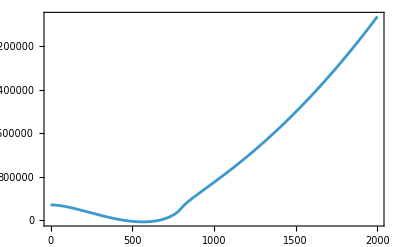

```mathematica
firaa=2000;
fitdat=Table[{p,sifu[ p]},{p,0,firaa,firaa/100}];
fifu=a(p^2-p0^2)^2+mm^2;
(*fifupa=FindFit[fitdat,fifu,{a,p0,mm},p]*)
Show[{ListLinePlot[fitdat,Frame->True](*,Plot[fifu/.fifupa,{p,0,firaa},PlotRange->All]*)}]
(*{Re[p],Im[p]}/.FindRoot[fifu/.fifupa,{p,1+1 ⅈ}]
{√Re[p^2],√Im[p^2]}/.FindRoot[fifu/.fifupa,{p,1+1 ⅈ}]*)
```

```mathematica
plotmu400T0=Plot3D[{Abs[sifu[p+ⅈ q ]]},{p,-1000,1000},{q,-1000,1000},PlotRange->{All,All,All},AxesLabel->{"Re p","Im p","Abs(1/Σ)"}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[1/sifu[p+100 ⅈ],{p,-300-0 ⅈ,300+800ⅈ}]
```

-Graphics3D-

```mathematica
datamu400T0=ParallelTable[Abs[sifu[p+ⅈ q]]//N,{p,-1000,1000,10},{q,-1000 ,1000,10}];
```

```mathematica
ListPlot3D[datamu400T0,PlotRange->All]
```

-Graphics3D-

```mathematica
Export["./mub400T1.dat",Abs[datamu400T0]]
```

./mub400T1.dat

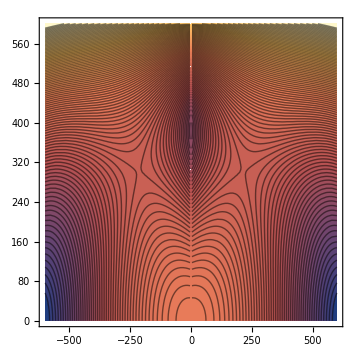

```mathematica
ComplexContourPlot[Abs[sifu[p]],{p,-600+0 ⅈ,600+600 ⅈ},Contours->100(*,Contours->{10^4,1.5*10^4,2*10^4,5*10^4,6*10^4,7*10^4,10^5,2*10^5,2.16*10^5,2.18*10^5,2.2*10^5,2.25*10^5,2.3*10^5,2.4*10^5,2.5*10^5,2.7*10^5,3*10^5,4*10^5,5*10^5,6*10^5,8*10^5,1*10^6}*),PlotRange->All]
```

#### fits

```mathematica
(*global*)
sipuxlist4=ParallelTable[{r,Re[sipux[r]]},{r,.005,.03,.02/200}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

798.978

281.805+707.165 ⅈ

(0.0664579 ⅇ^(-707.165 x))/x-(5.88506×10^-6 Sin[1.38105+798.978 x])/x^2.466

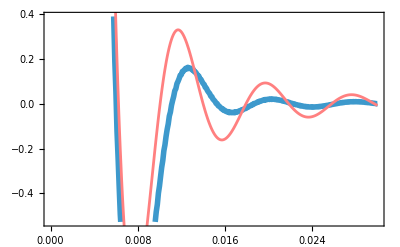

(0.0664579 ⅇ^(-707.165 x) Sin[0.658428+281.805 x])/x-(1.15074×10^-6 Sin[1.41489+798.978 x])/x^2.79339

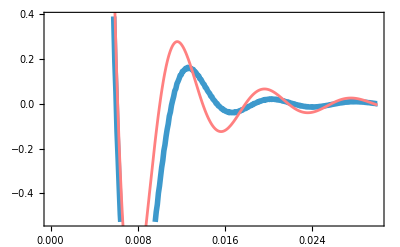

```mathematica
k0fix=2 pFT1[nnn]//N
ppole=p/.FindRoot[SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]],{p,1+ⅈ}]
(*testfunc33=a1/x ⅇ^(- c x)+a/x^a2 Sin[k0fix x+b1];
testfunc44=a1/x ⅇ^(- c x) Sin[c2 x+b2]+ (0 a)/x^a2 Sin[k0fix x+b1];*)
testfunc33=0.06645789744967699/x ⅇ^(- Im[ppole] x)+a2/x^c1 Sin[k0fix x+b1]-(0a3)/x^4 Sin[k0fix x+b2];
testfunc44=0.06645789744967699/x ⅇ^(- Im[ppole] x) Sin[Re[ppole] x+b3]+ a2/x^c1 Sin[k0fix x+b1]-(0a3)/x^4 Sin[k0fix x+b2];
(testfunc33/.FindFit[sipuxlist4,testfunc33,{a1, a2,a3,b1,b2,b3,c1,c2,d1},x,Method->NMinimize])
Show[ListPlot[sipuxlist4,Joined->True,Frame->True,PlotStyle->Thickness[.01]],Plot[%,{x,First[sipuxlist4][[1]],Last[sipuxlist4][[1]]},PlotStyle->Pink,PlotRange->All]]
(testfunc44/.FindFit[sipuxlist4,testfunc44,{a1, a2,a3,b1,b2,b3,c1,c2,d1},x,Method->NMinimize])
Show[ListPlot[sipuxlist4,Joined->True,Frame->True,PlotStyle->Thickness[.01]],Plot[%,{x,First[sipuxlist4][[1]],Last[sipuxlist4][[1]]},PlotStyle->Pink,PlotRange->All]]
```

798.978

{a1→2.11018×10^-7,b1→-1.80622,c1→3.00175}

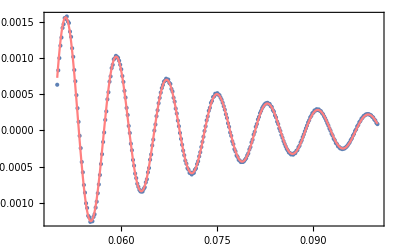

```mathematica
(* use large-r data to fit tail *)
rLmin=.05;
rLmax=.1;
sigrL=ParallelTable[{r,Re[sipux[r]]},{r,rLmin,rLmax,(rLmax-rLmin)/300}];
k0Fridel=2 pFT1[nnn]//N(*Fridel wave number*)
sigrLfit=a1/x^c1 Sin[k0Fridel x+b1];
fitparasL=FindFit[sigrL,sigrLfit,{a1, b1,c1},x,Method->NMinimize]
sigfitL=sigrLfit/.fitparasL;
Show[
ListPlot[sigrL,Frame->True],
Plot[sigfitL,{x,rLmin,rLmax},Frame->True,PlotStyle->Pink]
]
```

{a1→5.27269×10^-10,b1→3.03038,c1→4.40004}

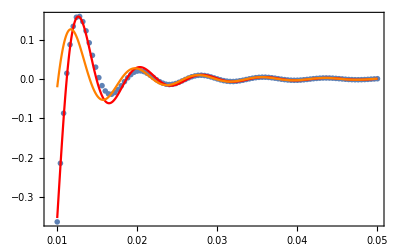

```mathematica
(* use large-r data to fit tail 2 *)
rLmin=.01;
rLmax=.05;
sigrL2=ParallelTable[{r,Re[sipux[r]]},{r,rLmin,rLmax,(rLmax-rLmin)/100}];
sigrLfit2=a1/x^c1 Sin[k0Fridel x+b1]+sigfitL;
fitparasL2=FindFit[sigrL2,sigrLfit2,{a1, b1,c1},x]
sigfitL2=sigrLfit2/.fitparasL2;
Show[
ListPlot[sigrL2,Frame->True,PlotMarkers->{Automatic,Scaled[0.035]},PlotRange->All],
Plot[{sigfitL2,sigfitL},{x,rLmin,rLmax},Frame->True,PlotStyle->{Red,Orange},PlotRange->All]
]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 400
     times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
                                                                        -34
     numerical integration. NIntegrate obtained 0.000013456 - 2.35511 10    I
                   -11
     and 5.90282 10    for the integral and error estimates.

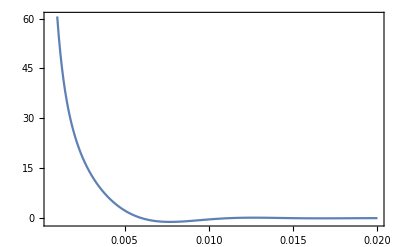

```mathematica
(* use smaller range in r to extract exponential piece *)
rSmin=.001;
rSmax=.02;
sigrS=ParallelTable[{r,Re[sipux[r]]},{r,rSmin,rSmax,(rSmax-rSmin)/200}];
ListPlot[sigrS,Frame->True,Joined->True,PlotRange->All]
```

281.805+707.165 ⅈ

{a1→0.420274,b1→1.98386}

{a1→0.525406,b1→1.,c1→1153.35}

{a1→0.20928,a2→0.000155398,b1→0.805105,b2→-1.55962,c1→1.82376}

{a1→0.206415,a2→-0.0000764262,b1→743.216,b2→1.66892,c1→1.96885}

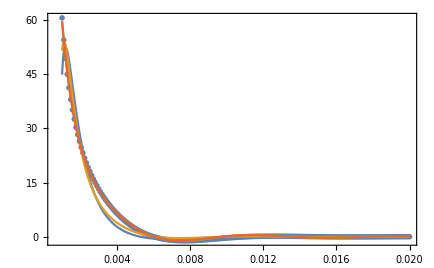

```mathematica
ppole=p/.FindRoot[SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]],{p,1+ⅈ}](*p-pole in the self-energy*)

sigrSfit=a1/x ⅇ^(- Im[ppole] x)Sin[Re[ppole] x+b1]+sigfitL;
fitparasS=FindFit[sigrS,sigrSfit,{a1, b1},x]
sigfitS=sigrSfit/.fitparasS;

sigrSfit2=a1/x ⅇ^(- c1 x)+sigfitL;
fitparasS2=FindFit[sigrS,sigrSfit2,{a1, b1,c1},x]
sigfitS2=sigrSfit2/.fitparasS2;

sigrSfit3=a1/x ⅇ^(- Im[ppole] x)Sin[Re[ppole] x+b1]+a2/x^c1 Sin[k0Fridel x+b2];
fitparasS3=FindFit[sigrS,sigrSfit3,{a1,a2, b1,b2,c1},x]
sigfitS3=sigrSfit3/.fitparasS3;

sigrSfit4=a1/x ⅇ^(- b1 x)+a2/x^c1 Sin[k0Fridel x+b2];
fitparasS4=FindFit[sigrS,sigrSfit4,{a1,a2, b1,b2,c1},x]
sigfitS4=sigrSfit4/.fitparasS4;

Show[
ListPlot[sigrS,Frame->True,PlotRange->All],
Plot[{sigfitS,sigfitS2,sigfitS3,sigfitS4},{x,rSmin,rSmax},Frame->True,PlotRange->All]
]
```

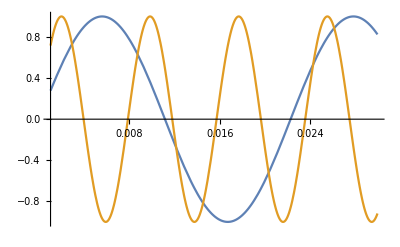

```mathematica
Plot[{Sin[Re[ppole] x],Sin[k0Fridel x]},{x,rSmin,rSmax}]
```

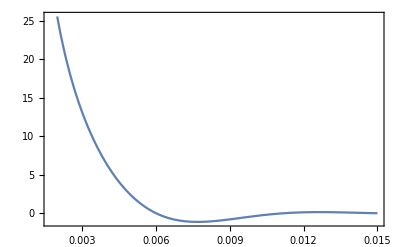

```mathematica
(*subtract long-distance tail*)
rSmin=.002;
rSmax=.015;
sigrS=ParallelTable[{r,Re[sipux[r]]},{r,rSmin,rSmax,(rSmax-rSmin)/200}];
ListPlot[sigrS,Frame->True,Joined->True,PlotRange->All]
```

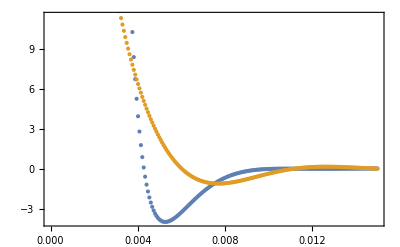

```mathematica
sigrSsub=Table[{sigrS[[n,1]],sigrS[[n,2]]-(sigfitL2/.x->sigrS[[n,1]])},{n,Length[sigrS]}];
ListPlot[{sigrSsub,sigrS},Frame->True]
```

281.805+707.165 ⅈ

{a1→6.25042,b1→8.31318}

{a1→20.9384,c1→1598.04}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a1→58.8955,b1→0.200284,c1→1006.02,c2→-46.7158}

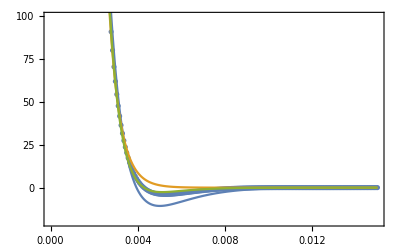

```mathematica
ppole=p/.FindRoot[SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]],{p,1+ⅈ}](*p-pole in the self-energy*)

sigrSsubfit=a1/x ⅇ^(- Im[ppole] x)Sin[Re[ppole] x+b1];
fitparasSsub=FindFit[sigrSsub,sigrSsubfit,{a1, b1},x]
sigfitSsub=sigrSsubfit/.fitparasSsub;

sigrSsubfit2=a1/x ⅇ^(- c1 x);
fitparasSsub2=FindFit[sigrSsub,sigrSsubfit2,{a1, c1},x]
sigfitSsub2=sigrSsubfit2/.fitparasSsub2;

sigrSsubfit3=a1/x ⅇ^(- c1 x) Sin[c2 x+b1];
fitparasSsub3=FindFit[sigrSsub,sigrSsubfit3,{a1, b1,c1,c2},x]
sigfitSsub3=sigrSsubfit3/.fitparasSsub3;

Show[
ListPlot[sigrSsub,Frame->True,PlotRange->{-20,100}],
Plot[{sigfitSsub,sigfitSsub2,sigfitSsub3},{x,rSmin,rSmax},Frame->True,PlotRange->All]
]
```

#### analytic structure μ=301 MeV

```mathematica
(* pole *)
sifu[p_]=SigmaPi[p,92.2204^2/2,mq0,301.];
(*FindRoot[sifu[p],{p,1+ⅈ}]
{√Abs[Re[p^2]],√Im[p^2]}/.%
FindMinimum[sifu[p],{p,200}]*)
```

{a→0.120348,p0→-653.72,mm→-7.66716×10^-6}

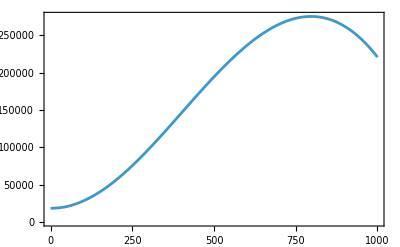

```mathematica
firaa=1000;
fitdat=Table[{p,Abs[sifu[p]]},{p,0,firaa,0.1}];
(*fifu=a(p-p0)^2+mm^2;*)
fifupa=FindFit[fitdat,fifu,{a,p0,mm},p]
Show[{ListLinePlot[fitdat,Frame->True]}]
```

```mathematica
ComplexPlot3D[sifu[p],{p,-1000 -1000 ⅈ,1000+1000 ⅈ},PlotRange->All]
```

-Graphics3D-

```mathematica
datamu301T0=ParallelTable[Abs[sifu[p+ⅈ q]]//N,{p,-1000 ,1000,10},{q,-1000 ,1000,10}];
```

```mathematica
Export["./mub301T0MSbar.dat",Abs[datamu301T0]]
```

./mub301T0MSbar.dat

```mathematica
ComplexContourPlot[Abs[sifu[p]],{p,-500 -1000 ⅈ,500+1000ⅈ},Contours->100,PlotRange->All]
```

-Graphics-

```mathematica
mub301T1data=ParallelTable[Abs[sifu[p+ⅈ q]]//N,{p,-800,800,5},{q,-800,800,5}];
Export["./mub301T1.dat",Re[mub301T1data]]
```

./mub301T1.dat

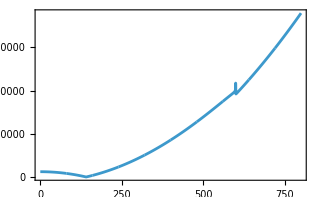

```mathematica
SigmaImTab=ParallelTable[{q,Abs[sifu[ⅈ q]]},{q,0,800,0.01}];
ListPlot[SigmaImTab,Frame->True,Joined->True]
```

```mathematica
2 √mq2/.{ρ->92.2204^2/2}//N
√mPi2/.{ρ->92.2204^2/2}//N
 pF/.{μ->301,ρ->92.2204^2/2}//N
```

599.433

300.001

27.7694

```mathematica
Abs[p+ⅈ q/.{p->-3.532769264436711*^-11,q->140.65326860618165}]
```

140.653

#### analytic structure μ=301 MeV renorm v2

```mathematica
(* pole *)
sifu[p_]=SigmaPi[p,92.2204^2/2,mq0,301.];
(*FindRoot[sifu[p],{p,1+ⅈ}]
{√Abs[Re[p^2]],√Im[p^2]}/.%
FindMinimum[sifu[p],{p,200}]*)
```

{a→1.00066,p0→-0.0752524,mm→134.837}

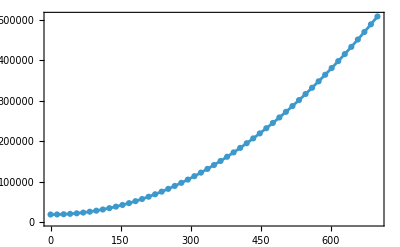

{-0.0752524,134.793}

{0.+134.793 ⅈ,0.+4.5041 ⅈ}

```mathematica
firaa=700;
fitdat=Table[{p,sifu[p]},{p,0,firaa,firaa/50}];
fifu=a(p-p0)^2+mm^2;
fifupa=FindFit[fitdat,fifu,{a,p0,mm},p]
Show[{ListPlot[fitdat,Frame->True],Plot[fifu/.fifupa,{p,0,firaa},PlotRange->All]}]
{Re[p],Im[p]}/.FindRoot[fifu/.fifupa,{p,1+1 ⅈ}]
{√Re[p^2],√Im[p^2]}/.FindRoot[fifu/.fifupa,{p,1+1 ⅈ}]
```

```mathematica
ComplexPlot3D[1/sifu[p],{p,-1000 -1000 ⅈ,1000+1000 ⅈ},PlotRange->All]
```

-Graphics3D-

```mathematica
ComplexContourPlot[Abs[sifu[p]],{p,-500 -1000 ⅈ,500+1000ⅈ},Contours->200,PlotRange->All]
```

-Graphics-

```mathematica
mub301T1data=ParallelTable[Abs[sifu[p+ⅈ q]]//N,{p,-1000,1000,10},{q,-1000,1000,10}];
Export["./mub301T1.dat",Re[mub301T1data]]
```

./mub301T1.dat

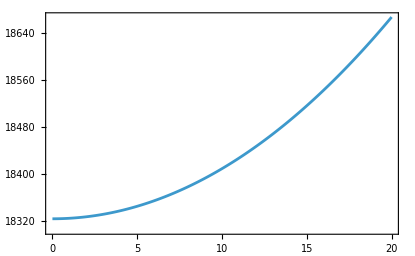

```mathematica
SigmaImTab=ParallelTable[{q,Abs[sifu[ q]]},{q,0,20,0.01}];
ListPlot[SigmaImTab,Frame->True,Joined->True]
```

#### fits2

```mathematica
(*global*)
sipuxlist4=ParallelTable[{r,Re[sipux[r]]//Quiet},{r,.005,0.5,0.0001}];
```

55.5388

-1.53821×10^-14+140.653 ⅈ

FindFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

(0.0859748 ⅇ^(-140.653 x))/x+(4.43548×10^-9 Sin[0.142771-55.5388 x])/x^4-(1.30835×10^-6 Sin[3.31419+55.5388 x])/x^2.60296

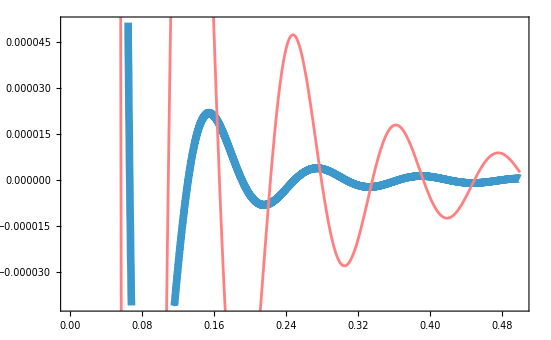

FindFit::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

-(5.52077×10^-8 Sin[0.190238-55.5388 x])/x^4-0.50205 x^17.2099 Sin[32.1521+55.5388 x]

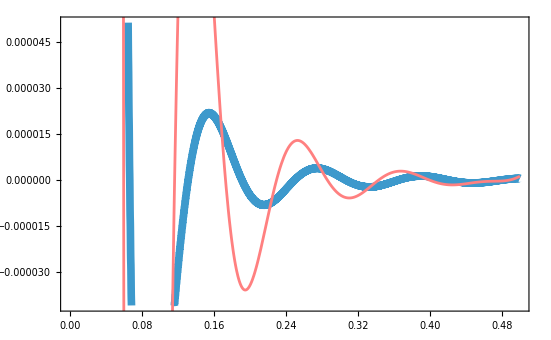

```mathematica
k0fix=2 pF/.{μ->301,ρ->92.2204^2/2}//N
ppole=p/.FindRoot[SigmaPi[p,92.2204^2/2,mq0,301.],{p,1+ⅈ}]
(*testfunc33=a1/x ⅇ^(- c x)+a/x^a2 Sin[k0fix x+b1];
testfunc44=a1/x ⅇ^(- c x) Sin[c2 x+b2]+ (0 a)/x^a2 Sin[k0fix x+b1];*)
testfunc33=a1/x ⅇ^(- Im[ppole] x)+a2/x^c1 Sin[k0fix x+b1]-a3/x^4 Sin[k0fix x+b2];
testfunc44=(*0.06645789744967699/x ⅇ^(- Im[ppole] x) Sin[Re[ppole] x+b3]*)+ a2/x^c1 Sin[k0fix x+b1]-a3/x^4 Sin[k0fix x+b2];
(testfunc33/.FindFit[sipuxlist4,testfunc33,{a1, a2,a3,a4,b1,b2,b3,c1(*,c2*)(*,d1*)},x(*,Method->NMinimize*)])
Show[ListPlot[sipuxlist4,Joined->True,Frame->True,PlotStyle->Thickness[.01]],Plot[%,{x,First[sipuxlist4][[1]],Last[sipuxlist4][[1]]},PlotStyle->Pink,PlotRange->All]]
(testfunc44/.FindFit[sipuxlist4,testfunc44,{a1, a2,a3,b1,b2,b3,c1,c2,d1},x(*,Method->NMinimize*)])
Show[ListPlot[sipuxlist4,Joined->True,Frame->True,PlotStyle->Thickness[.01]],Plot[%,{x,First[sipuxlist4][[1]],Last[sipuxlist4][[1]]},PlotStyle->Pink,PlotRange->All]]
```

```mathematica
(* use large-r data to fit tail *)
rLmin=.05;
rLmax=.1;
sigrL=ParallelTable[{r,Re[sipux[r]]},{r,rLmin,rLmax,(rLmax-rLmin)/300}];
k0Fridel=2 pFT1[nnn]//N(*Fridel wave number*)
sigrLfit=a1/x^c1 Sin[k0Fridel x+b1];
fitparasL=FindFit[sigrL,sigrLfit,{a1, b1,c1},x,Method->NMinimize]
sigfitL=sigrLfit/.fitparasL;
Show[
ListPlot[sigrL,Frame->True],
Plot[sigfitL,{x,rLmin,rLmax},Frame->True,PlotStyle->Pink]
]
```

798.978

{a1→2.11018×10^-7,b1→-1.80622,c1→3.00175}

-Graphics-

```mathematica
(* use large-r data to fit tail 2 *)
rLmin=.01;
rLmax=.05;
sigrL2=ParallelTable[{r,Re[sipux[r]]},{r,rLmin,rLmax,(rLmax-rLmin)/100}];
sigrLfit2=a1/x^c1 Sin[k0Fridel x+b1]+sigfitL;
fitparasL2=FindFit[sigrL2,sigrLfit2,{a1, b1,c1},x]
sigfitL2=sigrLfit2/.fitparasL2;
Show[
ListPlot[sigrL2,Frame->True,PlotMarkers->{Automatic,Scaled[0.035]},PlotRange->All],
Plot[{sigfitL2,sigfitL},{x,rLmin,rLmax},Frame->True,PlotStyle->{Red,Orange},PlotRange->All]
]
```

{a1→5.27269×10^-10,b1→3.03038,c1→4.40004}

-Graphics-

```mathematica
(* use smaller range in r to extract exponential piece *)
rSmin=.001;
rSmax=.02;
sigrS=ParallelTable[{r,Re[sipux[r]]},{r,rSmin,rSmax,(rSmax-rSmin)/200}];
ListPlot[sigrS,Frame->True,Joined->True,PlotRange->All]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 400
     times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
                                                                        -34
     numerical integration. NIntegrate obtained 0.000013456 - 2.35511 10    I
                   -11
     and 5.90282 10    for the integral and error estimates.

-Graphics-

```mathematica
ppole=p/.FindRoot[SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]],{p,1+ⅈ}](*p-pole in the self-energy*)

sigrSfit=a1/x ⅇ^(- Im[ppole] x)Sin[Re[ppole] x+b1]+sigfitL;
fitparasS=FindFit[sigrS,sigrSfit,{a1, b1},x]
sigfitS=sigrSfit/.fitparasS;

sigrSfit2=a1/x ⅇ^(- c1 x)+sigfitL;
fitparasS2=FindFit[sigrS,sigrSfit2,{a1, b1,c1},x]
sigfitS2=sigrSfit2/.fitparasS2;

sigrSfit3=a1/x ⅇ^(- Im[ppole] x)Sin[Re[ppole] x+b1]+a2/x^c1 Sin[k0Fridel x+b2];
fitparasS3=FindFit[sigrS,sigrSfit3,{a1,a2, b1,b2,c1},x]
sigfitS3=sigrSfit3/.fitparasS3;

sigrSfit4=a1/x ⅇ^(- b1 x)+a2/x^c1 Sin[k0Fridel x+b2];
fitparasS4=FindFit[sigrS,sigrSfit4,{a1,a2, b1,b2,c1},x]
sigfitS4=sigrSfit4/.fitparasS4;

Show[
ListPlot[sigrS,Frame->True,PlotRange->All],
Plot[{sigfitS,sigfitS2,sigfitS3,sigfitS4},{x,rSmin,rSmax},Frame->True,PlotRange->All]
]
```

281.805+707.165 ⅈ

{a1→0.420274,b1→1.98386}

{a1→0.525406,b1→1.,c1→1153.35}

{a1→0.20928,a2→0.000155398,b1→0.805105,b2→-1.55962,c1→1.82376}

{a1→0.206415,a2→-0.0000764262,b1→743.216,b2→1.66892,c1→1.96885}

-Graphics-

```mathematica
Plot[{Sin[Re[ppole] x],Sin[k0Fridel x]},{x,rSmin,rSmax}]
```

-Graphics-

```mathematica
(*subtract long-distance tail*)
rSmin=.002;
rSmax=.015;
sigrS=ParallelTable[{r,Re[sipux[r]]},{r,rSmin,rSmax,(rSmax-rSmin)/200}];
ListPlot[sigrS,Frame->True,Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
sigrSsub=Table[{sigrS[[n,1]],sigrS[[n,2]]-(sigfitL2/.x->sigrS[[n,1]])},{n,Length[sigrS]}];
ListPlot[{sigrSsub,sigrS},Frame->True]
```

-Graphics-

```mathematica
ppole=p/.FindRoot[SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]],{p,1+ⅈ}](*p-pole in the self-energy*)

sigrSsubfit=a1/x ⅇ^(- Im[ppole] x)Sin[Re[ppole] x+b1];
fitparasSsub=FindFit[sigrSsub,sigrSsubfit,{a1, b1},x]
sigfitSsub=sigrSsubfit/.fitparasSsub;

sigrSsubfit2=a1/x ⅇ^(- c1 x);
fitparasSsub2=FindFit[sigrSsub,sigrSsubfit2,{a1, c1},x]
sigfitSsub2=sigrSsubfit2/.fitparasSsub2;

sigrSsubfit3=a1/x ⅇ^(- c1 x) Sin[c2 x+b1];
fitparasSsub3=FindFit[sigrSsub,sigrSsubfit3,{a1, b1,c1,c2},x]
sigfitSsub3=sigrSsubfit3/.fitparasSsub3;

Show[
ListPlot[sigrSsub,Frame->True,PlotRange->{-20,100}],
Plot[{sigfitSsub,sigfitSsub2,sigfitSsub3},{x,rSmin,rSmax},Frame->True,PlotRange->All]
]
```

281.805+707.165 ⅈ

{a1→6.25042,b1→8.31318}

{a1→20.9384,c1→1598.04}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a1→58.8955,b1→0.200284,c1→1006.02,c2→-46.7158}

-Graphics-

#### analytic structure μ=290 MeV

```mathematica
(* pole *)
sifu[p_]=SigmaPi[p,92.2204^2/2,mq0,290.];
(*FindRoot[sifu[p],{p,1+ⅈ}]
{√Abs[Re[p^2]],√Im[p^2]}/.%
FindMinimum[sifu[p],{p,200}]*)
```

#### fits3

```mathematica
(*global*)
sipuxlist4=ParallelTable[{r,Re[sipux[r]]//Quiet},{r,.01,0.2,0.002}];
```

2.92963×10^-15+140.653 ⅈ

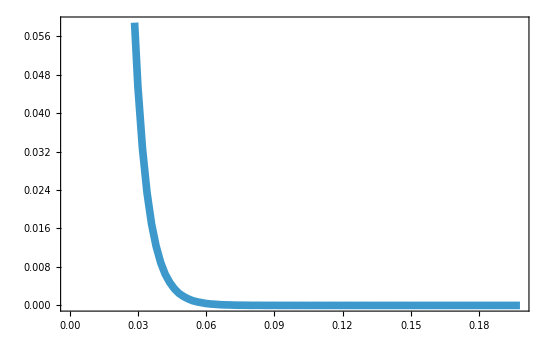

```mathematica
k0fix=2 pF/.{μ->301,ρ->92.2204^2/2}//N;
ppole=p/.FindRoot[SigmaPi[p,92.2204^2/2,mq0,301.],{p,1+ⅈ}]
(*testfunc33=a1/x ⅇ^(- c x)+a/x^a2 Sin[k0fix x+b1];
testfunc44=a1/x ⅇ^(- c x) Sin[c2 x+b2]+ (0 a)/x^a2 Sin[k0fix x+b1];*)
testfunc33=a1/x ⅇ^(- Im[ppole] x)+a2/x^c1 Sin[k0fix x+b1]-a3/x^4 Sin[k0fix x+b2];
testfunc44=(*0.06645789744967699/x ⅇ^(- Im[ppole] x) Sin[Re[ppole] x+b3]*)+ a2/x^c1 Sin[k0fix x+b1]-(0a3)/x^4 Sin[k0fix x+b2];
Show[ListPlot[sipuxlist4,Joined->True,Frame->True,PlotStyle->Thickness[.01]],Plot[%,{x,First[sipuxlist4][[1]],Last[sipuxlist4][[1]]},PlotStyle->Pink,PlotRange->All]]
```

```mathematica
(* use large-r data to fit tail *)
rLmin=.05;
rLmax=.1;
sigrL=ParallelTable[{r,Re[sipux[r]]},{r,rLmin,rLmax,(rLmax-rLmin)/300}];
k0Fridel=2 pFT1[nnn]//N(*Fridel wave number*)
sigrLfit=a1/x^c1 Sin[k0Fridel x+b1];
fitparasL=FindFit[sigrL,sigrLfit,{a1, b1,c1},x,Method->NMinimize]
sigfitL=sigrLfit/.fitparasL;
Show[
ListPlot[sigrL,Frame->True],
Plot[sigfitL,{x,rLmin,rLmax},Frame->True,PlotStyle->Pink]
]
```

798.978

{a1→2.11018×10^-7,b1→-1.80622,c1→3.00175}

-Graphics-

```mathematica
(* use large-r data to fit tail 2 *)
rLmin=.01;
rLmax=.05;
sigrL2=ParallelTable[{r,Re[sipux[r]]},{r,rLmin,rLmax,(rLmax-rLmin)/100}];
sigrLfit2=a1/x^c1 Sin[k0Fridel x+b1]+sigfitL;
fitparasL2=FindFit[sigrL2,sigrLfit2,{a1, b1,c1},x]
sigfitL2=sigrLfit2/.fitparasL2;
Show[
ListPlot[sigrL2,Frame->True,PlotMarkers->{Automatic,Scaled[0.035]},PlotRange->All],
Plot[{sigfitL2,sigfitL},{x,rLmin,rLmax},Frame->True,PlotStyle->{Red,Orange},PlotRange->All]
]
```

{a1→5.27269×10^-10,b1→3.03038,c1→4.40004}

-Graphics-

```mathematica
(* use smaller range in r to extract exponential piece *)
rSmin=.001;
rSmax=.02;
sigrS=ParallelTable[{r,Re[sipux[r]]},{r,rSmin,rSmax,(rSmax-rSmin)/200}];
ListPlot[sigrS,Frame->True,Joined->True,PlotRange->All]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::eincr: 
   The global error of the strategy GlobalAdaptive has increased more than 400
     times. The global error is expected to decrease monotonically after a
     number of integrand evaluations. Suspect one of the following: the
     working precision is insufficient for the specified precision goal; the
     integrand is highly oscillatory or it is not a (piecewise) smooth
     function; or the true value of the integral is 0. Increasing the value of
     the GlobalAdaptive option MaxErrorIncreases might lead to a convergent
                                                                        -34
     numerical integration. NIntegrate obtained 0.000013456 - 2.35511 10    I
                   -11
     and 5.90282 10    for the integral and error estimates.

-Graphics-

```mathematica
ppole=p/.FindRoot[SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]],{p,1+ⅈ}](*p-pole in the self-energy*)

sigrSfit=a1/x ⅇ^(- Im[ppole] x)Sin[Re[ppole] x+b1]+sigfitL;
fitparasS=FindFit[sigrS,sigrSfit,{a1, b1},x]
sigfitS=sigrSfit/.fitparasS;

sigrSfit2=a1/x ⅇ^(- c1 x)+sigfitL;
fitparasS2=FindFit[sigrS,sigrSfit2,{a1, b1,c1},x]
sigfitS2=sigrSfit2/.fitparasS2;

sigrSfit3=a1/x ⅇ^(- Im[ppole] x)Sin[Re[ppole] x+b1]+a2/x^c1 Sin[k0Fridel x+b2];
fitparasS3=FindFit[sigrS,sigrSfit3,{a1,a2, b1,b2,c1},x]
sigfitS3=sigrSfit3/.fitparasS3;

sigrSfit4=a1/x ⅇ^(- b1 x)+a2/x^c1 Sin[k0Fridel x+b2];
fitparasS4=FindFit[sigrS,sigrSfit4,{a1,a2, b1,b2,c1},x]
sigfitS4=sigrSfit4/.fitparasS4;

Show[
ListPlot[sigrS,Frame->True,PlotRange->All],
Plot[{sigfitS,sigfitS2,sigfitS3,sigfitS4},{x,rSmin,rSmax},Frame->True,PlotRange->All]
]
```

281.805+707.165 ⅈ

{a1→0.420274,b1→1.98386}

{a1→0.525406,b1→1.,c1→1153.35}

{a1→0.20928,a2→0.000155398,b1→0.805105,b2→-1.55962,c1→1.82376}

{a1→0.206415,a2→-0.0000764262,b1→743.216,b2→1.66892,c1→1.96885}

-Graphics-

```mathematica
Plot[{Sin[Re[ppole] x],Sin[k0Fridel x]},{x,rSmin,rSmax}]
```

-Graphics-

```mathematica
(*subtract long-distance tail*)
rSmin=.002;
rSmax=.015;
sigrS=ParallelTable[{r,Re[sipux[r]]},{r,rSmin,rSmax,(rSmax-rSmin)/200}];
ListPlot[sigrS,Frame->True,Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
sigrSsub=Table[{sigrS[[n,1]],sigrS[[n,2]]-(sigfitL2/.x->sigrS[[n,1]])},{n,Length[sigrS]}];
ListPlot[{sigrSsub,sigrS},Frame->True]
```

-Graphics-

```mathematica
ppole=p/.FindRoot[SigmaPi[p,rhoT1dat[[nnn]],mq0,mudat[[nnn]]],{p,1+ⅈ}](*p-pole in the self-energy*)

sigrSsubfit=a1/x ⅇ^(- Im[ppole] x)Sin[Re[ppole] x+b1];
fitparasSsub=FindFit[sigrSsub,sigrSsubfit,{a1, b1},x]
sigfitSsub=sigrSsubfit/.fitparasSsub;

sigrSsubfit2=a1/x ⅇ^(- c1 x);
fitparasSsub2=FindFit[sigrSsub,sigrSsubfit2,{a1, c1},x]
sigfitSsub2=sigrSsubfit2/.fitparasSsub2;

sigrSsubfit3=a1/x ⅇ^(- c1 x) Sin[c2 x+b1];
fitparasSsub3=FindFit[sigrSsub,sigrSsubfit3,{a1, b1,c1,c2},x]
sigfitSsub3=sigrSsubfit3/.fitparasSsub3;

Show[
ListPlot[sigrSsub,Frame->True,PlotRange->{-20,100}],
Plot[{sigfitSsub,sigfitSsub2,sigfitSsub3},{x,rSmin,rSmax},Frame->True,PlotRange->All]
]
```

281.805+707.165 ⅈ

{a1→6.25042,b1→8.31318}

{a1→20.9384,c1→1598.04}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a1→58.8955,b1→0.200284,c1→1006.02,c2→-46.7158}

-Graphics-

## T> 0 mean-field

### pion self-energy at p_0=0

```mathematica
nF[x_]=1/(ⅇ^(x/T)+1);
Eq=√(q^2+mq2);
Eqp=√(q^2+p^2-2 p q x+mq2);
Eqpp=√(q^2+p^2+2 p q x+mq2);

PiTInt[p_,ρ_,T_,μ_]=1/Eq (-nF[Eq-μ]-nF[Eq+μ])-p^2/(4 Eq Eqp) ((nF[Eqp-μ]+nF[Eq+μ])/(-Eq-Eqp)+(-nF[Eq-μ]-nF[Eqp+μ])/(Eq+Eqp)+(-nF[Eq+μ]+nF[Eqp+μ])/(-Eq+Eqp)+(nF[Eq-μ]-nF[Eqp-μ])/(Eq-Eqp));
PiTIntF[p_,ρ_,T_,μ_]=1/(2 Eq) (-nF[Eq-μ]-nF[Eq+μ])-1/2 p^2/(4 Eq Eqpp) ((nF[Eqpp-μ]+nF[Eq+μ])/(-Eq-Eqpp)-(nF[Eq-μ]+nF[Eqpp+μ])/(Eq+Eqpp)+(nF[Eq-μ]-nF[Eqpp-μ])/(Eq-Eqpp)-(nF[Eq+μ]-nF[Eqpp+μ])/(-Eq+Eqpp));


qmax=10^5;
PiPiMedT[p_?NumberQ,ρ_?NumberQ,T_?NumberQ,μ_?NumberQ]:=-h^2 Nc (2π)/(2 π)^3 NIntegrate[q^2 PiTInt[p,ρ,T,μ],{q,0,qmax},{x,-1,1},(*WorkingPrecision->20,AccuracyGoal->20,PrecisionGoal->20,*)
Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->10];
PiPiMedTF[p_?NumberQ,ρ_?NumberQ,T_?NumberQ,μ_?NumberQ]:=-2 h^2 Nc (2π)/(2 π)^3 NIntegrate[q^2 PiTIntF[p,ρ,T,μ],{q,0,qmax},{x,-1,1}(*,WorkingPrecision->20*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0},MaxRecursion->10];
SigmaPiVacRen2[p_,ρ_,Λ_]=PiPiVacRen1[p,ρ,Λ]+p^2+mPi2-(PiPiVacRen1[p,ρ0,Λ]-PiPiVacRen1p0[ρ0,Λ])(*//Simplify*);
SigmaPiT[p_?NumberQ,ρ_?NumberQ,T_?NumberQ,μ_?NumberQ,Λ_?NumberQ]:=SigmaPiVacRen2[p,ρ,Λ]+PiPiMedT[p,ρ,T,μ]
```

#### T=2

400

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

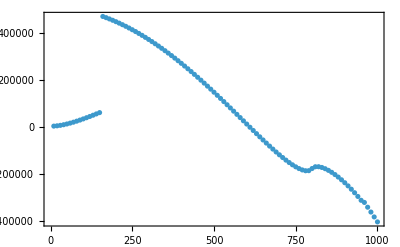

```mathematica
ntest=80;
mudat[[ntest]]
ptest=900;
Ttest=10.;
rhoT2dat=6.035325968608047^2/2;
SigmaPiT2[p_?NumberQ]:=SigmaPiT[p,rhoT2dat,1.,400.,300.](*+p^2-ν + λ rhoT2dat*);
SigmaTab2=ParallelTable[{p,SigmaPiT2[p]//Quiet},{p,10,1000,10}];
ListPlot[SigmaTab2,Frame->True]
```

```mathematica
sigcomptab2=Flatten[ParallelTable[{p,q,SigmaPiT2[p+ⅈ q]//Quiet},{p,10,1000,10},{q,10,100,10}],1];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

$Aborted

```mathematica
plotT2=ListPlot3D[{Abs[sigcomptab2]},PlotRange->All,AxesLabel->{"Re p","Im p","Abs[Re1/Σ_π]"},ViewPoint->{-2,-2,2}]
```

-Graphics3D-

```mathematica
Export["./Resigma.pdf",plotT2]
```

./Resigma.pdf

```mathematica
plotcon=ListContourPlot[sigcomptab2,Contours->700,PlotRange->All]
```

```mathematica
sigcomptab2v2=Flatten[ParallelTable[{p,q,Re[1/SigmaPiT2[p+ⅈ q]]//Quiet},{p,500,1200,10},{q,10,500,10}],1];
ListPlot3D[sigcomptab2v2,PlotRange->All]
```

LinkObject::linkd: 无法使用关闭的连接 LinkObject["C:\Program Files\Wolfram Research\Wolfram\14.2\WolframKernel" -noicon -noinit -subkernel -wstp,4007,71] 进行通讯.

KernelObject::rdead: Discarding kernel 56 (Local (42)).

LaunchKernels::clone: dead kernel 56 (Local (42)) resurrected as kernel 67 (Local (42)).

ListPlot3D::arrayerr: sigcomptab2v2 必须是一个有效数组或者由有效数组组成的列表.

ListPlot3D[sigcomptab2v2,PlotRange→All]

#### T=10 renorm_1

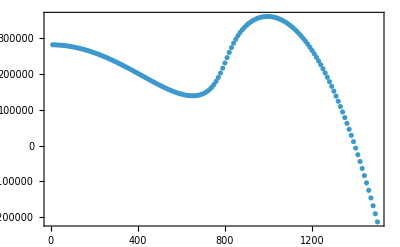

```mathematica
ntest=80;
mudat[[ntest]];
ptest=900;
Ttest=10.;
rhoT10dat=6.035325968608047^2/2;

SigmaPiT10[p_?NumberQ]:=SigmaPiT[p,rhoT10dat,10.,400.,300.];
SigmaTab10=ParallelTable[{p,SigmaPiT10[p]//Quiet},{p,10,1500,10}];
ListPlot[SigmaTab10,Frame->True]
```

```mathematica
sigcomptab10=ParallelTable[{Abs[SigmaPiT10[p+ⅈ q]]//Quiet},{p,-1000,1000,10},{q,-1000,1000,10}];
```

```mathematica
ListPlot3D[sigcomptab10[[All,All,1]],PlotRange->All]
```

-Graphics3D-

```mathematica
plotcon=ListContourPlot[Transpose[sigcomptab10[[All,All,1]]],Contours->100,PlotRange->All]
```

-Graphics-

```mathematica
Export["./mu400T10_MSb.dat",sigcomptab10[[All,All,1]]]
```

./mu400T10_MSb.dat

```mathematica
Dimensions[sigcomptab10[[All,All,1]]]
```

{201,201}

#### T=10 renorm_2

```mathematica
ntest=80;
mudat[[ntest]];
ptest=900;
Ttest=10.;
rhoT10dat=6.035325968608047^2/2;

SigmaPiT10[p_?NumberQ]:=SigmaPiT[p,rhoT10dat,10.,400.,300.];
SigmaTab10=ParallelTable[{p,√SigmaPiT10[p]//Quiet},{p,10,1500,10}];
ListPlot[SigmaTab10,Frame->True]
```

-Graphics-

```mathematica
sigcomptab10=ParallelTable[{Abs[1/SigmaPiT10[p+ⅈ q]]//Quiet},{p,-1000,1000,10},{q,-1000,1000,10}];
ListPlot3D[sigcomptab10[[All,All,1]],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[sigcomptab10[[All,All,1]],PlotRange->All,AxesLabel->{"Im p","Re p","Abs(1/Σ) MSbar+vacuum sub"},Ticks->{{{200,1000},{150,500},{100,0},{50,-500},{0,-1000}},{{200,-1000},{150,-500},{100,0},{50,500},{0,1000}}}]
```

-Graphics3D-

```mathematica
plotcon=ListContourPlot[sigcomptab10[[All,All,1]],Contours->100,PlotRange->All]
```

-Graphics-

```mathematica
Export["./mu400T10_MSbpVS.dat",sigcomptab10[[All,All,1]]]
```

./mu400T10_MSbpVS.dat

#### T=30

```mathematica
ntest=80;
mudat[[ntest]]
ptest=900;
Ttest=30;

SigmaPiT30[p_?NumberQ]:=SigmaPiT[p,rhoT30dat[[ntest]],Ttest,mudat[[ntest]],mq0];
pFT30[n_]:=pF/.{μ->mudat[[n]],ρ->rhoT30dat[[n]]};
pFT30[ntest]//N

SigmaTab30=ParallelTable[{p,SigmaPiT30[p]//Quiet},{p,10,600,1}];
ListPlot[SigmaTab30,Frame->True]
```

400

399.521

-Graphics-

```mathematica
NMinimize[Abs[SigmaPiT30[ⅈ q]],q]//Quiet
NMinimize[Abs[SigmaPiT30[q]],q]//Quiet
```

{290139.,{q→-0.0000144312}}

```mathematica
NMinimize[Abs[SigmaPiT30[p+ⅈ q]],{p,q}]//Quiet
```

{245648.,{p→406.434,q→25.9315}}

```mathematica
sigImtab30=ParallelTable[{q,Re[SigmaPiT30[ⅈ q]]//Quiet},{q,1,5000,10}];
ListPlot[sigImtab30]
```

-Graphics-

```mathematica
sigcomptab30=Flatten[ParallelTable[{p,q,Re[1/SigmaPiT30[p+ⅈ q]]//Quiet},{p,10,1000,10},{q,10,2000,10}],1];
ListPlot3D[sigcomptab30,PlotRange->All]
```

-Graphics3D-

```mathematica
plotcon=ListContourPlot[sigcomptab30,Contours->700,PlotRange->All]
```

-Graphics-

```mathematica
Export["./mub400T30.pdf",plotcon]
```

./mub400T30.pdf

```mathematica
Export["./sigcomptab30.dat",sigcomptab30]
```

./sigcomptab30.dat

```mathematica
pbound2=10^7;
plow=10^-2;
t30rangeFT=Join[Range[plow,1200,(1200-plow)/400],Range[1210,pbound2,(pbound2-1210)/400]];
SigmaTabFT=ParallelTable[{p,SigmaPiT[p,rhoT30dat[[ntest]],Ttest,mudat[[ntest]],mq0]//Quiet},{p,t30rangeFT}];
```

```mathematica
sit30fit=Interpolation[SigmaTabFT];
Show[ListLogLogPlot[SigmaTabFT,PlotStyle->Pink,Frame->True],LogLogPlot[sit30fit[p],{p,plow,pbound2}]]
```

-Graphics-

```mathematica
sipuxT[r_]:=NIntegrate[p/(2 π^2) Sin[p r]/r 1/sit30fit[p],{p,plow,pbound2},MaxRecursion->100(*,WorkingPrecision->20*)];
sipuxlistT30=ParallelTable[{r,Re[sipuxT[r]]},{r,2 10^-2,6 10^-2,5 10^-2/100}];
ListPlot[{sipuxlistT30},Joined->True,Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
2 pF/.{ρ->ρ0,μ->mudat[[ntest]]}//N
2 pF/.{ρ->ρ0,μ->mudat[[80]]}//N
```

0.

529.15

```mathematica
testfunc33= a ⅇ^(- c x)+a2/x^b2 Sin[a1 400 x+b1];
testfunc44=a ⅇ^(- c x) Sin[400 x+b1];

(testfunc33/.FindFit[sipuxlistT30,testfunc33,{a,a1, a2,b1,b2,c},x])
Show[ListPlot[sipuxlistT30,Joined->True,Frame->True,PlotStyle->Thickness[.01],PlotRange->All],Plot[%,{x,First[sipuxlistT30][[1]],Last[sipuxlistT30][[1]]},PlotStyle->Pink,PlotRange->All]]

(testfunc44/.FindFit[sipuxlistT30,testfunc44,{a,a1, a2,b1,b2,c},x])
Show[ListPlot[sipuxlistT30,Joined->True,Frame->True,PlotStyle->Thickness[.01],PlotRange->All],Plot[%,{x,First[sipuxlistT30][[1]],Last[sipuxlistT30][[1]]},PlotStyle->Pink,PlotRange->All]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-0.0219379 ⅇ^(-2143.9 x)-(2.81926×10^-16 Sin[13.7147-965.352 x])/x^7.6928

-Graphics-

-709649. ⅇ^(-896.553 x) Sin[1.20878+400 x]

-Graphics-

```mathematica
SigmaPiT[138 ⅈ,rhoT30dat[[ntest]],30,mudat[[ntest]],mq0]
√SigmaPiT[1,rhoT30dat[[ntest]],30,mudat[[ntest]],mq0]
```

43.762-7.24039×10^-17 ⅈ

137.822

```mathematica
√SigmaPiT[1,rhoT30dat[[ntest]],Ttest,mudat[[ntest]],mq0]
```

538.645

#### T=100

```mathematica
ntest=80;
mudat[[ntest]]
ptest=900;
Ttest=100;

SigmaPiT100[p_?NumberQ]:=SigmaPiT[p,rhoT100dat[[ntest]],Ttest,mudat[[ntest]],mq0];
pFT100[n_]:=pF/.{μ->mudat[[n]],ρ->rhoT100dat[[n]]};
pFT100[ntest]//N

SigmaTab=ParallelTable[{p,SigmaPiT100[p]},{p,10,600,10}];
ListPlot[SigmaTab,Frame->True]
```

400

399.734

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

-Graphics-

```mathematica
NMinimize[Abs[SigmaPiT100[p+ⅈ q]],{p,q}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -70185.4+43514.1 ⅈ and 0.168777 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -71453.+44433.9 ⅈ and 0.179541 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -97341.1+38147.9 ⅈ and 0.120988 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{368118.,{p→323.096,q→16.017}}

```mathematica
pbound2=10^8;
plow=10^-3;
t100rangeFT=Join[Range[plow,1200,(1200-plow)/300],Range[1210,pbound2,(pbound2-1210)/300]];
SigmaTabFT=ParallelTable[{p,SigmaPiT[p,rhoT100dat[[ntest]],Ttest,mudat[[ntest]],mq0]//Quiet},{p,t100rangeFT}];
```

```mathematica
sit100fit=Interpolation[SigmaTabFT];
Show[LogLogPlot[sit100fit[p],{p,plow,pbound2},Frame->True],ListLogLogPlot[SigmaTabFT,PlotStyle->Pink,Frame->True]]
```

-Graphics-

```mathematica
sipuxT[r_]:=NIntegrate[p/(2 π^2) Sin[p r]/r 1/sit100fit[p],{p,plow,pbound2},MaxRecursion->100(*,WorkingPrecision->40*)]//Quiet;
rMinT=0.001;
rMaxT=0.02;
sipuxlistT100=ParallelTable[{r,Re[sipuxT[r]]},{r,rMinT,rMaxT,(rMaxT-rMinT)/100}];
ListPlot[{sipuxlistT100},Joined->True,Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{sipuxlistT100},Joined->True,Frame->True]
```

-Graphics-

```mathematica
testfunc33=a ⅇ^(- c x)+a2/x^2 Sin[a1 500 x+b1];
testfunc44=a ⅇ^(- c x) Sin[a1 500 x+b1];

(testfunc33/.FindFit[sipuxlistT100,testfunc33,{a,a1, a2,b1,b2,c},x])
Show[ListPlot[sipuxlistT100,Joined->True,Frame->True,PlotStyle->Thickness[.01],PlotRange->All],Plot[%,{x,First[sipuxlistT100][[1]],Last[sipuxlistT100][[1]]},PlotStyle->Pink,PlotRange->All]]

(testfunc44/.FindFit[sipuxlistT100,testfunc44,{a,a1, a2,b1,b2,c},x])
Show[ListPlot[sipuxlistT100,Joined->True,Frame->True,PlotStyle->Thickness[.01],PlotRange->All],Plot[%,{x,First[sipuxlistT100][[1]],Last[sipuxlistT100][[1]]},PlotStyle->Pink,PlotRange->All]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

-0.0156023 ⅇ^(-236.176 x)-(5.26608×10^-8 Sin[2.29453-639.161 x])/x^2

-Graphics-

9.7606 ⅇ^(-504.212 x) Sin[0.546138+492.117 x]

-Graphics-

```mathematica
530/2
```

265

```mathematica
√(2 ρ0)//N
```

92.3077

```mathematica
pF/.{ρ->ρ0,μ->400}//N
```

264.575

#### pure moat toymodel

```mathematica
sdasd=10^-5 (p^2-300^2)^2+200^2;
Plot[sdasd,{p,0,500},PlotRange->All,AxesOrigin->{0,0}]
sdasdr[r_]:=NIntegrate[p/(2 π^2) Sin[p r]/r 1/sdasd,{p,0,pbound2},MaxRecursion->100,WorkingPrecision->20];
sdasdrtab=Table[{r,sdasdr[r]},{r,6 10^-2,14 10^-2,8 10^-2/100}];
ListPlot[sdasdrtab,Joined->True,PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
testfunc44=a ⅇ^(- c 138 x) Sin[a1 300 x+b1];
(testfunc44/.FindFit[sdasdrtab,testfunc44,{a,a1, a2,b1,b2,c},x])
Show[ListPlot[sdasdrtab,Joined->True,Frame->True,PlotStyle->Thickness[.01],PlotRange->All],Plot[%,{x,First[sdasdrtab][[1]],Last[sdasdrtab][[1]]},PlotStyle->Pink,PlotRange->All]]
```

4.8691657159043436726 ⅇ^(-114.1772961542058829 x) Sin[0.011079909720561023979+316.08163173394496449 x]

-Graphics-

#### comparison finite T vs T=0

```mathematica
ntest=80;
SigmaTab1=ParallelTable[{p,SigmaPiT[p,rhoT1dat[[ntest]],1,mudat[[ntest]],mq0]},{p,10,1000,20}];
SigmaTab30=ParallelTable[{p,SigmaPiT[p,rhoT30dat[[ntest]],30,mudat[[ntest]],mq0]},{p,10,1000,20}];

Show[{Plot[{SigmaPi[p,rhoT1dat[[ntest]],mq0,mudat[[ntest]]]},{p,0,1000},Frame->True],ListPlot[{SigmaTab1,SigmaTab30},Frame->True]}]
```

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«2 more identical outputs»

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«5 more identical outputs»

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«2 more identical outputs»

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«1 more identical outputs»

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

-Graphics-

### Shi’s version

```mathematica
mf2[h_,ρ_]:=(h^2 ρ)/2;
nff[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)-μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)-μ)/T]+1)];
nfa[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)+μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)+μ)/T]+1)];
F1[q_,ρ_,h_,T_,μ_]:=q^2/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=q^2/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])));
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^2 NIntegrate[(2F1[q,ρ,h,T,μ]-(p0^2+ps^2)F1F1m[q,p0,ps,x,ρ,h,T,μ]),{q,0.,500.,5000.},{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+(p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5])-(Nc h^2 mf2[h,ρ])/(16 π^2);
gammavac2[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5]);
gamma2[p0_,ps_,ρ_,ρ0_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ]+gammavac[p0,ps,ρ,h,Mmass,MZ]-gammavac2[p0,ps,ρ0,h,Mmass,MZ]+p0^2+ps^2+(λ300 ρ+ν300);
λ300=75.8;
ν300=-482.^2;
```

```mathematica
SigmaTabShi=ParallelTable[{p,gamma2[0,p,rhoT30dat[[ntest]],ρ0,h,30,mudat[[ntest]],300,300]},{p,10,600,10}];
ListPlot[{SigmaTabShi,SigmaTab},Frame->True]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

-Graphics-